```mathematica
Vcoulomb=PotentialSmearing[Cij α/r]
```

(Cij α Erf[r σ])/r

```mathematica
Vstring=PotentialSmearing[-3/4 Cij*b*r]
```

-(3 b Cij ((2 ⅇ^(-r^2 σ^2) r σ)/(√π)+(1+2 r^2 σ^2) Erf[r σ]))/(8 r σ^2)

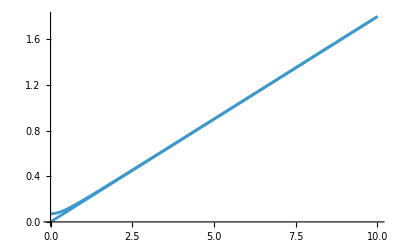

```mathematica
Plot[{Vstring,-3/4 Cij*b*r}/.{b->0.18,σ->2.853,Cij->-4/3},{r,0,10}]
```

```mathematica
Vscreen1=PotentialSmearing[-3/4 Cij*b1*(1-Exp[-μ*r])/μ]
```

-(3 b1 Cij ⅇ^(-r μ) σ (4 ⅇ^(r μ) r σ^2+ⅇ^(μ^2/(4 σ^2)) (μ-2 r σ^2) Erfc[(μ-2 r σ^2)/(2 √(σ^2))]-ⅇ^(1/4 μ (8 r+μ/σ^2)) (μ+2 r σ^2) Erfc[(μ+2 r σ^2)/(2 √(σ^2))]))/(16 r μ (σ^2)^(3/2))

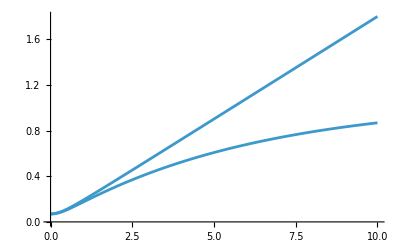

```mathematica
Plot[{Vstring,Vscreen1}/.{b->0.18,b1->0.18,σ->2.853,μ->0.169,Cij->-4/3},{r,0,10}]
```

```mathematica
Vscreen2=PotentialSmearing[-3/4 Cij*b2*(1-Exp[-μ*r^2])/μ]
```

-(3 b2 Cij σ (1/(√(σ^2))-(ⅇ^(-(r^2 μ σ^2)/(μ+σ^2)) σ^2)/((μ+σ^2)^(3/2))))/(4 μ)

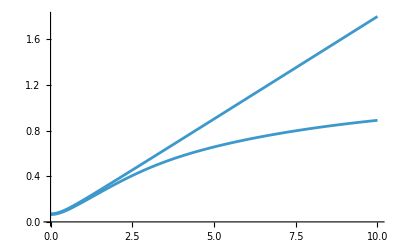

```mathematica
Plot[{Vstring,Vscreen1+Vscreen2}/.{b->0.18,b1->0.16,b2->0.02,σ->2.853,μ->0.169,Cij->-4/3},{r,0,10}]
```

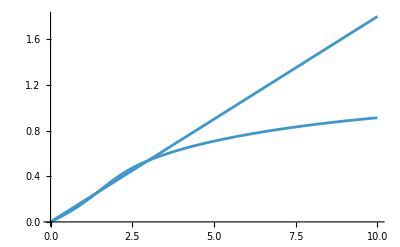

```mathematica
Plot[{-3/4 Cij(b1*(1-Exp[-μ*r^1])/μ)-3/4 Cij(b2*(1-Exp[-μ*r^2])/μ)-3/4 Cij(b3*(1-Exp[-μ*r^3])/μ),-3/4 Cij*b*r}
/.{b->0.18,b1->0.14,b2->0.02,b3->0.02,σ->2.853,μ->0.169,Cij->-4/3},{r,0,10}]
```

```mathematica
SphericalLaplacian[Cij α/r Erf[σ*r]]//Simplify
```

-(4 Cij ⅇ^(-r^2 σ^2) α σ^3)/(√π)

{3,3}

{{-0.630063-0.465546 (4.05378 ⅇ^(-7.43396 r^2)+0.388187 ⅇ^(-1.88495 r^2)+0.0297806 ⅇ^(-0.2421 r^2))-4/3 ((0.25 Erf[0.492037 r])/r+(0.15 Erf[1.37294 r])/r+(0.2 Erf[2.72653 r])/r)+(0.0588996 ⅇ^(-0.140163 r) (30.6472 ⅇ^(0.140163 r) r+1.00064 (0.140163-15.3236 r) Erfc[0.180636 (0.140163-15.3236 r)]-ⅇ^(0.0350408 (0.0182938+8 r)) (0.140163+15.3236 r) Erfc[0.180636 (0.140163+15.3236 r)]))/r}}

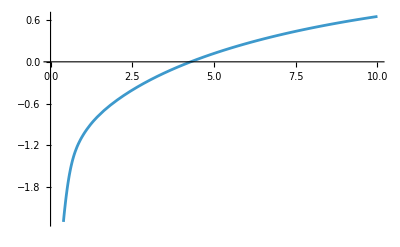

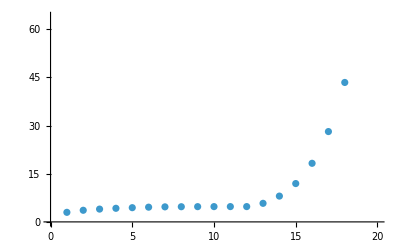

{2.97658,3.61926,3.98498,4.23428,4.42721,4.58558,4.6828,4.72346,4.74899,4.75908,4.76289,4.76518,5.78096,8.03367,11.9358,18.2411,28.1235,43.41,67.2502,106.688}

```mathematica
{f1,f2}={3,3}
{S,L,J}={0,0,0};
{Nmax,Rmax,Rmin}={20,20.0,0.01};
Vij=Potential[{f1,f2},{S,L,J},"GIScreen"]
Plot[Vij,{r,0,10}]
{e,v}=MesonGEM[{f1,f2},{S,L,J},{Nmax,Rmax,Rmin},"GIScreen"];
ListPlot[e]
e
```

```mathematica
Table[GetRMSRadius[n,L,{Nmax,Rmax,Rmin},v],{n,1,Nmax}]
```

{0.321404,0.689093,1.07455,1.49627,2.253,3.53386,5.27783,7.66228,11.5754,17.7931,28.0005,7.34935,0.718941,0.384694,0.23349,0.148325,0.0962771,0.0630076,0.0409026,0.0252753}

-1.16624 ⅇ^(-3.89386 r^2)+2.65628 ⅇ^(-2.66075 r^2)-5.13222 ⅇ^(-1.81815 r^2)+6.67169 ⅇ^(-1.24238 r^2)-8.50321 ⅇ^(-0.848944 r^2)+8.80751 ⅇ^(-0.580102 r^2)-9.55137 ⅇ^(-0.396396 r^2)+8.90926 ⅇ^(-0.270866 r^2)-8.70498 ⅇ^(-0.185088 r^2)+7.73963 ⅇ^(-0.126475 r^2)-6.77244 ⅇ^(-0.0864228 r^2)+5.6218 ⅇ^(-0.0590545 r^2)-4.45298 ⅇ^(-0.0403532 r^2)+3.3604 ⅇ^(-0.0275742 r^2)-2.42216 ⅇ^(-0.018842 r^2)+1.67537 ⅇ^(-0.0128752 r^2)-1.11825 ⅇ^(-0.00879786 r^2)+0.723984 ⅇ^(-0.00601177 r^2)-0.456421 ⅇ^(-0.00410797 r^2)+0.280765 ⅇ^(-0.00280706 r^2)-0.168514 ⅇ^(-0.00191812 r^2)+0.0984207 ⅇ^(-0.00131069 r^2)-0.0555928 ⅇ^(-0.000895625 r^2)+0.0300336 ⅇ^(-0.000611999 r^2)-0.0152382 ⅇ^(-0.000418192 r^2)+0.00705478 ⅇ^(-0.000285759 r^2)-0.00284832 ⅇ^(-0.000195265 r^2)+0.000931744 ⅇ^(-0.000133429 r^2)-0.000216452 ⅇ^(-0.0000911749 r^2)+0.0000262825 ⅇ^(-0.0000623017 r^2)

-1.93951

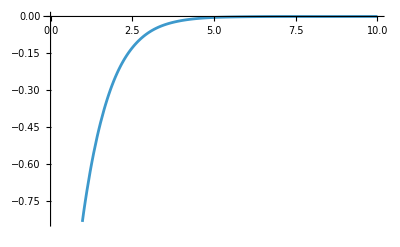

```mathematica
gwv=GetGEMRnlr[1,L,{Nmax,Rmax,Rmin},v]
gwv/.{r->0}
Plot[gwv,{r,0,10}]
```

0.865308

1.2092 ⅇ^(-0.374379 r^2)

1.2092

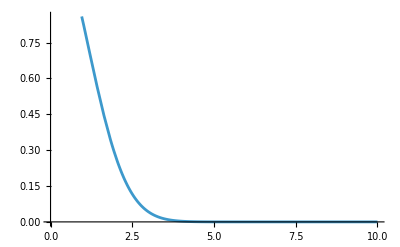

```mathematica
beta=GetSHOBeta[1,L,{Nmax,Rmax,Rmin},v]
swv=GetSHORnlr[1,L,beta]
swv/.{r->0}
Plot[swv,{r,0,10}]
```